## Elliptical parametrizations

An elliptical mode can be written as the sum of two R/L circularly polarized modes. In terms of h ≡ h_+-i h_× , for a monochromatic mode this is
	h=1/(√2)(C_R e^(-i ω t)+C_L^*e^(i ω t))≡ 1/(√2)(A_R e^(-i (ω t-ϕ_R))+A_L e^(i (ω t-ϕ_L))) ,
where the C_(R/L)≡A_(R/L) e^(iϕ_(R/L)) are complex valued, but A_(R/L) are real. This is clearly written in terms of circular, R/L modes. We can rewrite this in terms of an ellipticity and related angles as follows:
	h=1/2 A [(1+ϵ) e^(-i (ω t-ϕ_R))+(1-ϵ) e^(i (ω t-ϕ_L))] ,
or, equivalently,
	h=A_[cosθ  cos(ω t-ϕ) - ϵ sinθ  sin(ω t-ϕ)] - i A [sinθ  cos(ω t-ϕ) + ϵ cosθ  sin(ω t-ϕ)] .
We could also replace {A,ϵ} with {Â=A √(1+ϵ^2),χ=arctan ϵ} to get another equivalent expression,
	h=OverHat[A_][cosχ cosθ  cos(ω t-ϕ) - sinχ  sinθ  sin(ω t-ϕ)] - i Â [cosχ sinθ  cos(ω t-ϕ) + sinχ  cosθ  sin(ω t-ϕ)] .
	
With some algebra, we can further show this to be equivalent to a template based on linear modes,
	h= ((A^+)_x cos ω t + (A^+)_y sin ω t)-i ((A^×)_x cos ω t + (A^×)_y sin ω t),
which is the same as
	h= A^+cos (ω t -φ^+) - i A^×cos (ω t -φ^×)e^(-t/τ_n).

### Coordinate transformations

The relevant coordinate transformations are as follows, suppressing the n index.

```mathematica
AepToAchi={
A->Ahat Cos[χ],
ϵ->Tan[χ]
};
AchiToAep={
Ahat->A Sqrt[1+ϵ^2],
χ->ArcTan[ϵ]
};
```

```mathematica
AepToCphi={
A-> (CR+CL)/Sqrt[2],
ϵ-> (CR -CL)/(CR+CL),
θ->(ϕL-ϕR)/2,
ϕ->(ϕL+ϕR)/2
};
CphiToAep={
CR->1/(√2) A (1+ϵ),
CL->1/(√2) A(1- ϵ),
ϕR->ϕ-θ,
ϕL->θ+ϕ
};
```

```mathematica
AphiToAxAy={
Ap->√(Apx^2+Apy^2),
Ac->√(Acx^2+Acy^2),
φp->ArcTan[Apx,Apy],
φc->ArcTan[Acx,Acy]
};
AxAyToAphi={
Apx->Ap Cos[φp],
Apy->Ap Sin[φp],
Acx->Ac Cos[φc],
Acy->Ac Sin[φc]
};

AxAyToCphi={
Apx->(CR Cos[ϕR]+CL Cos[ϕL])/Sqrt[2],
Apy->(CR Sin[ϕR]+CL Sin[ϕL])/Sqrt[2],
Acx->(-CR Sin[ϕR]+CL Sin[ϕL])/Sqrt[2],
Acy->(CR Cos[ϕR]-CL Cos[ϕL])/Sqrt[2]
};
```

#### Circular and linear amplitudes

Let’s find the inverse transformation for the last set:

```mathematica
(*Assuming[{Element[{Apx,Apy,Acx,Acy},Reals],CR>0,CL>0,0≤ϕR≤2π,0≤ϕL≤2π},
FullSimplify[Solve[Equal@@@Flatten[AxAyToCphi],{CR,CL,ϕR,ϕL}]]] *)
```

Unsurprisingly, there are multiple solutions. We know the right one from Jones geometry.

```mathematica
CphiToAxAy={
CR->1/(√2) √((Apy-Acx)^2+(Apx+Acy)^2),
CL->1/(√2) √((Apy+Acx)^2+(Apx-Acy)^2),
ϕR->ArcTan[Apx+Acy,Apy-Acx],
ϕL->ArcTan[Apx-Acy,Apy+Acx]
};
```

The corresponding transformation to (A, φ) is:

```mathematica
CphiToAphi=Assuming[{Ac>0,Ap>0,Element[{ϕp,ϕc},Reals]},FullSimplify[CphiToAxAy//.AxAyToAphi]]
```

{CR→(√(Ac^2+Ap^2+2 Ac Ap Sin[φc-φp]))/(√2),CL→(√(Ac^2+Ap^2-2 Ac Ap Sin[φc-φp]))/(√2),ϕR→ArcTan[Ap Cos[φp]+Ac Sin[φc],-Ac Cos[φc]+Ap Sin[φp]],ϕL→ArcTan[Ap Cos[φp]-Ac Sin[φc],Ac Cos[φc]+Ap Sin[φp]]}

Is there a nice transformation directly from (A,φ) to (A,ϵ)?

```mathematica
FullSimplify[AepToCphi/.CphiToAphi,{Ap>0, Ac>0,0<=φp<2π,0<=φc<2π}]
```

{A→1/2 (√(Ac^2+Ap^2-2 Ac Ap Sin[φc-φp])+√(Ac^2+Ap^2+2 Ac Ap Sin[φc-φp])),ϵ→((Ac^2+Ap^2-√(Ac^4+Ap^4+2 Ac^2 Ap^2 Cos[2 φc-2 φp])) Csc[φc-φp])/(2 Ac Ap),θ→1/2 (ArcTan[Ap Cos[φp]-Ac Sin[φc],Ac Cos[φc]+Ap Sin[φp]]-ArcTan[Ap Cos[φp]+Ac Sin[φc],-Ac Cos[φc]+Ap Sin[φp]]),ϕ→1/2 (ArcTan[Ap Cos[φp]-Ac Sin[φc],Ac Cos[φc]+Ap Sin[φp]]+ArcTan[Ap Cos[φp]+Ac Sin[φc],-Ac Cos[φc]+Ap Sin[φp]])}

Not really nice.

#### Linear quadratures

We will also want to be able to go directly from linear quadratures to the elliptic parameterization (or vice-versa):

```mathematica
AepToAxAy =Simplify[AepToCphi//.CphiToAxAy]
```

{A→1/2 (√((Acy+Apx)^2+(Acx-Apy)^2)+√((Acy-Apx)^2+(Acx+Apy)^2)),ϵ→(√((Acy+Apx)^2+(Acx-Apy)^2)-√((Acy-Apx)^2+(Acx+Apy)^2))/(√((Acy+Apx)^2+(Acx-Apy)^2)+√((Acy-Apx)^2+(Acx+Apy)^2)),θ→1/2 (ArcTan[-Acy+Apx,Acx+Apy]-ArcTan[Acy+Apx,-Acx+Apy]),ϕ→1/2 (ArcTan[-Acy+Apx,Acx+Apy]+ArcTan[Acy+Apx,-Acx+Apy])}

```mathematica
FullSimplify[AepToAxAy //.AxAyToAphi]
```

{A→1/2 (√(Ac^2+Ap^2-2 Ac Ap Sin[φc-φp])+√(Ac^2+Ap^2+2 Ac Ap Sin[φc-φp])),ϵ→1/(2 Ac Ap)Csc[φc-φp] (Ac^2+Ap^2-√(Ac^2+Ap^2-2 Ac Ap Sin[φc-φp]) √(Ac^2+Ap^2+2 Ac Ap Sin[φc-φp])),θ→1/2 (ArcTan[Ap Cos[φp]-Ac Sin[φc],Ac Cos[φc]+Ap Sin[φp]]-ArcTan[Ap Cos[φp]+Ac Sin[φc],-Ac Cos[φc]+Ap Sin[φp]]),ϕ→1/2 (ArcTan[Ap Cos[φp]-Ac Sin[φc],Ac Cos[φc]+Ap Sin[φp]]+ArcTan[Ap Cos[φp]+Ac Sin[φc],-Ac Cos[φc]+Ap Sin[φp]])}

What’s the transformation in the other direction?

```mathematica
FullSimplify[AxAyToCphi]
```

{Apx→(CL Cos[ϕL]+CR Cos[ϕR])/(√2),Apy→(CL Sin[ϕL]+CR Sin[ϕR])/(√2),Acx→(CL Sin[ϕL]-CR Sin[ϕR])/(√2),Acy→(-CL Cos[ϕL]+CR Cos[ϕR])/(√2)}

```mathematica
FullSimplify[AxAyToCphi//.CphiToAep,{Element[{χ,θ,ϕ},Reals],A>0,-1<=ϵ<=1}]//MatrixForm
```

(Apx→A (Cos[θ] Cos[ϕ]+ϵ Sin[θ] Sin[ϕ])
Apy→-A ϵ Cos[ϕ] Sin[θ]+A Cos[θ] Sin[ϕ]
Acx→A (Cos[ϕ] Sin[θ]-ϵ Cos[θ] Sin[ϕ])
Acy→A (ϵ Cos[θ] Cos[ϕ]+Sin[θ] Sin[ϕ]))

```mathematica
FullSimplify[(AxAyToCphi//.CphiToAep//.AepToAchi),{Element[{χ,θ,ϕ},Reals],Ahat>0}]//MatrixForm
```

(Apx→Ahat (Cos[θ] Cos[ϕ] Cos[χ]+Sin[θ] Sin[ϕ] Sin[χ])
Apy→Ahat (Cos[θ] Cos[χ] Sin[ϕ]-Cos[ϕ] Sin[θ] Sin[χ])
Acx→Ahat (Cos[ϕ] Cos[χ] Sin[θ]-Cos[θ] Sin[ϕ] Sin[χ])
Acy→Ahat (Cos[χ] Sin[θ] Sin[ϕ]+Cos[θ] Cos[ϕ] Sin[χ]))

#### Alternative in terms of χ

Is this anything simpler in terms of χ? First look at the circular amplitudes:

```mathematica
AchiToCphi=FullSimplify[AchiToAep//.AepToCphi,{CL>0,CR>0}]
```

{Ahat→√(CL^2+CR^2),χ→ArcTan[1-(2 CL)/(CL+CR)]}

```mathematica
CphiToAchi=FullSimplify[TrigReduce[CphiToAep//.AepToAchi],{-1<=ϵ<=1,-Pi/4<χ<Pi/4}]
```

{CR→(Ahat (Cos[χ]+Sin[χ]))/(√2),CL→(Ahat (Cos[χ]-Sin[χ]))/(√2),ϕR→-θ+ϕ,ϕL→θ+ϕ}

Now look at the linear quadratures in terms of χ:

```mathematica
AxAys = {Apx,Apy,Acx,Acy};
FullSimplify[AchiToAep//.AepToAxAy,Element[AxAys,Reals]]
```

{Ahat→√(Acx^2+Acy^2+Apx^2+Apy^2),χ→ArcTan[(Acx^2+Acy^2+Apx^2+Apy^2-√(((Acy+Apx)^2+(Acx-Apy)^2) ((Acy-Apx)^2+(Acx+Apy)^2)))/(2 Acy Apx-2 Acx Apy)]}

```mathematica
FullSimplify[AxAyToCphi/.CphiToAchi,{-1<=ϵ<=1,-Pi/4<χ<Pi/4}]
```

{Apx→Ahat (Cos[θ] Cos[ϕ] Cos[χ]+Sin[θ] Sin[ϕ] Sin[χ]),Apy→Ahat (Cos[θ] Cos[χ] Sin[ϕ]-Cos[ϕ] Sin[θ] Sin[χ]),Acx→Ahat (Cos[ϕ] Cos[χ] Sin[θ]-Cos[θ] Sin[ϕ] Sin[χ]),Acy→Ahat (Cos[χ] Sin[θ] Sin[ϕ]+Cos[θ] Cos[ϕ] Sin[χ])}

### Transformation checks

Let’s check that the above transformations return the expected expressions for h.

```mathematica
hRL=(CR Exp[I ϕR] Exp[-I ωt]+CL Exp[-I ϕL] Exp[I ωt])/Sqrt[2];
```

In terms of an ellipticity, the complex-valued strain should look like h=1/2 A [(1+ϵ) e^(-i(ωt-ϕ_R))+(1-ϵ) e^(i (ω_n t-ϕ_L))] , with ϕ_R=ϕ-θ and  ϕ_L=ϕ+θ

```mathematica
hAep = hRL//.CphiToAep
```

((A ⅇ^(-ⅈ (θ+ϕ)+ⅈ ωt) (1-ϵ))/(√2)+(A ⅇ^(ⅈ (-θ+ϕ)-ⅈ ωt) (1+ϵ))/(√2))/(√2)

```mathematica
FullSimplify[hAep -1/2 A((1+ϵ) Exp[-I(ωt-ϕR)]+(1-ϵ) Exp[I(ωt-ϕL)])//.CphiToAep]
```

0

Look at the corresponding plus and cross polarizations, which should take the form
	h_+=A [cosθ cos(ωt-ϕ) - ϵ sinθ  sin(ωt-ϕ)] 
	h_×=A [sinθ cos(ωt-ϕ) + ϵ cosθ  sin(ωt-ϕ)]

```mathematica
Assuming[{Element[{A,θ,ϕ,ϵ,ωt},Reals]},FullSimplify[ComplexExpand[Re[hAep]]]]
Assuming[{Element[{A,θ,ϕ,ϵ,ωt},Reals]},FullSimplify[ComplexExpand[-Im[hAep]]]]
```

A (Cos[θ] Cos[ϕ-ωt]+ϵ Sin[θ] Sin[ϕ-ωt])

A (Cos[ϕ-ωt] Sin[θ]-ϵ Cos[θ] Sin[ϕ-ωt])

Now, focus on the cos and sin quadratures of the linear polarizations. First, check that we get the right expressions starting from h= A^+cos (ωt -φ^+) - i A^×cos (ωt -φ^×)

```mathematica
hAphi = Ap Cos[ωt -φp]-I Ac Cos[ωt -φc];
hAphi//.AphiToAxAy
```

-ⅈ √(Acx^2+Acy^2) Cos[ωt-ArcTan[Acx,Acy]]+√(Apx^2+Apy^2) Cos[ωt-ArcTan[Apx,Apy]]

Simplifying, we should get  h=((A^+)_x cos ωt+(A^+)_y sin ωt)-i((A^×)_x cos ωt+(A^×)_y sin ωt)

```mathematica
hAxAy=ComplexExpand[FullSimplify[hAphi//.AphiToAxAy]]
```

Apx Cos[ωt]+Apy Sin[ωt]+ⅈ (-Acx Cos[ωt]-Acy Sin[ωt])

We should be able to re-express this in terms of the original R/L modes, i.e. h=C_R e^(-i (ωt-ϕ_R))+C_L e^(i (ωt+ϕ_L))

```mathematica
TrigToExp[hAxAy//.AxAyToCphi]
Simplify[TrigToExp[hAxAy//.AxAyToCphi] - hRL]
```

(CR ⅇ^(ⅈ ϕR-ⅈ ωt))/(√2)+(CL ⅇ^(-ⅈ ϕL+ⅈ ωt))/(√2)

0

The inverse transformation is

```mathematica
FullSimplify[(hRL//.CphiToAxAy)-hAxAy]
```

0

Or, straight to (A,φ),

```mathematica
FullSimplify[(hRL//.CphiToAphi)-hAphi]
```

0

```mathematica
FullSimplify[(hAphi//.AphiToAxAy//.AxAyToCphi)]
FullSimplify[(hAphi//.AphiToAxAy//.AxAyToCphi)-hRL]
```

(ⅇ^(-ⅈ (ϕL+ωt)) (CR ⅇ^(ⅈ (ϕL+ϕR))+CL ⅇ^(2 ⅈ ωt)))/(√2)

0

Our transformations work! :)

Just to be extra sure, double check the intermediate expression for R/L modes in terms of linear polarizations and cos/sin quadratures:

```mathematica
ComplexExpand[TrigExpand[ExpToTrig[hRL]]]
```

(CL Cos[ϕL] Cos[ωt])/(√2)+(CR Cos[ϕR] Cos[ωt])/(√2)+(CL Sin[ϕL] Sin[ωt])/(√2)+(CR Sin[ϕR] Sin[ωt])/(√2)+ⅈ (-(CL Cos[ωt] Sin[ϕL])/(√2)+(CR Cos[ωt] Sin[ϕR])/(√2)+(CL Cos[ϕL] Sin[ωt])/(√2)-(CR Cos[ϕR] Sin[ωt])/(√2))

```mathematica
AphiToAep = AphiToAxAy//.AxAyToCphi//.CphiToAep;
AepToAphi = Simplify[AepToCphi//.CphiToAphi];
```

### Jacobians

Now that we’ve nailed down the transformations between all possible parametrizations, let’s compute some Jacobians.

```mathematica
Aeps = {A,ϵ,θ,ϕ};
```

#### Intensity amplitude

First, let’s look at the transformation from {Â,χ} to {A,ϵ}. We want to compute the following Jacobian:
	J = |(∂(A, ϵ, θ, ϕ))/(∂(Â, χ, θ, ϕ))|

```mathematica
Achis = {Ahat,χ,θ,ϕ};
```

```mathematica
dAchi=Assuming[Element[Aeps,Reals],FullSimplify[Det[D[Aeps//.AepToAchi,{Achis}]]]]
```

Sec[χ]

Simple! we just need a Jacobian of sec χ=Â/A. In terms of the target quantities this is

```mathematica
JAchi=Assuming[{A>0,-1<=ϵ<=1},FullSimplify[Abs[dAchi]//.AchiToAep]]
```

√(1+ϵ^2)

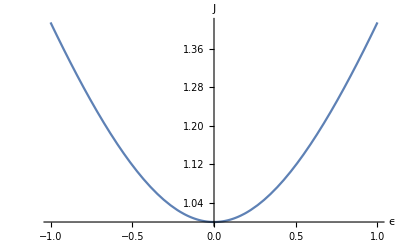

```mathematica
fig = Plot[JAchi,{ϵ,-1,1},AxesLabel->{"ϵ","J"}, PlotRange->Full]
```

```mathematica
Export["jac_Aeps_Achi.pdf",fig]
```

jac_Aeps_Achi.pdf

```mathematica
ellip =Tan[RandomVariate[UniformDistribution[{-Pi/4,Pi/4}],1000000]];
```

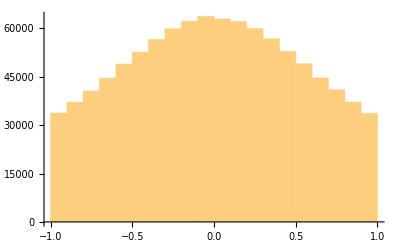

```mathematica
Histogram[ellip]
```

#### Coordinate degeneracies

Let’s try to understand what the true degeneracies are for the canonical parametrization.

```mathematica
ComplexExpand[FullSimplify[hAep/.A->1/.ωt->1]]
```

Cos[θ] Cos[1-ϕ]-ϵ Sin[θ] Sin[1-ϕ]+ⅈ (-Cos[1-ϕ] Sin[θ]-ϵ Cos[θ] Sin[1-ϕ])

```mathematica
transf={θ->θp+Pi,ϵ->ϵp,ϕ->ϕp+Pi,A->1,ωt->1};
ComplexExpand[FullSimplify[hAep//.transf]]
```

Cos[θp] Cos[1-ϕp]-ϵp Sin[θp] Sin[1-ϕp]+ⅈ (-Cos[1-ϕp] Sin[θp]-ϵp Cos[θp] Sin[1-ϕp])

Now look at the intensity amplitude and χ:

```mathematica
hAchi = Ahat ((Cos[χ]Cos[θ]Cos[ωt-ϕ]-Sin[χ]Sin[θ]Sin[ωt-ϕ])-I (Cos[χ]Sin[θ]Cos[ωt-ϕ]+Sin[χ]Cos[θ]Sin[ωt-ϕ]))
```

Ahat (Cos[θ] Cos[χ] Cos[ϕ-ωt]+Sin[θ] Sin[χ] Sin[ϕ-ωt]-ⅈ (Cos[χ] Cos[ϕ-ωt] Sin[θ]-Cos[θ] Sin[χ] Sin[ϕ-ωt]))

```mathematica
ComplexExpand[FullSimplify[hAchi]]
```

1/2 Ahat Cos[θ] Cos[ϕ-χ-ωt]+1/2 Ahat Cos[θ] Cos[ϕ+χ-ωt]+1/2 Ahat Cos[ϕ-χ-ωt] Sin[θ]-1/2 Ahat Cos[ϕ+χ-ωt] Sin[θ]+ⅈ (1/2 Ahat Cos[θ] Cos[ϕ-χ-ωt]-1/2 Ahat Cos[θ] Cos[ϕ+χ-ωt]-1/2 Ahat Cos[ϕ-χ-ωt] Sin[θ]-1/2 Ahat Cos[ϕ+χ-ωt] Sin[θ])

```mathematica
transf={θ->θp+Pi,χ->χp,ϕ->ϕp+Pi,A->1};
ComplexExpand[FullSimplify[hAchi//.transf]]
```

1/2 Ahat Cos[θp] Cos[ϕp-χp-ωt]+1/2 Ahat Cos[θp] Cos[ϕp+χp-ωt]+1/2 Ahat Cos[ϕp-χp-ωt] Sin[θp]-1/2 Ahat Cos[ϕp+χp-ωt] Sin[θp]+ⅈ (1/2 Ahat Cos[θp] Cos[ϕp-χp-ωt]-1/2 Ahat Cos[θp] Cos[ϕp+χp-ωt]-1/2 Ahat Cos[ϕp-χp-ωt] Sin[θp]-1/2 Ahat Cos[ϕp+χp-ωt] Sin[θp])

#### Circular amplitudes

We want to compute the following Jacobian:
	J = |(∂(A, ϵ, θ, ϕ))/(∂(C_R, C_L, ϕ_R,ϕ_L))|

```mathematica
Cphis = {CR,CL,ϕR,ϕL};
```

```mathematica
dCphi=Assuming[Element[Aeps,Reals],FullSimplify[Det[D[Aeps//.AepToCphi,{Cphis}]]]]
```

1/(√2 (CL+CR))

```mathematica
JCphi=Assuming[{A>0,-1<=ϵ<=1},FullSimplify[Abs[dCphi]//.CphiToAep]]
```

1/(2 A)

How about the χ parametrization?

```mathematica
Achis//.AchiToCphi//.AepToCphi
```

{√(CL^2+CR^2),ArcTan[1-(2 CL)/(CL+CR)],(ϕL-ϕR)/2,(ϕL+ϕR)/2}

```mathematica
dCphi2 =Assuming[Element[Achis,Reals],FullSimplify[Det[D[Achis//.AchiToCphi//.AepToCphi,{Cphis}]]]]
```

1/(2 √(CL^2+CR^2))

```mathematica
JCphi2=Assuming[{Ahat>0,-π/4<=χ<=π/4},FullSimplify[Abs[dCphi2]//.CphiToAchi]]
```

1/(2 Ahat)

#### Linear amplitudes

We want to compute the following Jacobian:
	J = |(∂(A, ϵ, θ, ϕ))/(∂(A_+,A_×,φ_+,φ_×))|

```mathematica
Aphis= {Ap,Ac,φp,φc};
```

```mathematica
dAphi=Assuming[{Element[Aeps,Reals],Ap>0,Ac>0},FullSimplify[Det[D[Aeps//.AepToAphi,{Aphis}]]]]
```

(2 Ac Ap)/(√(Ac^4+Ap^4+2 Ac^2 Ap^2 Cos[2 φc-2 φp]) (√(Ac^2+Ap^2-2 Ac Ap Sin[φc-φp])+√(Ac^2+Ap^2+2 Ac Ap Sin[φc-φp])))

```mathematica
JAphi=FullSimplify[dAphi//.AphiToAep,{Element[Aeps,Reals],A>0,-1<ϵ<1}]
```

(√(((1+ϵ^2)^2)/((-1+ϵ^2)^2)-Cos[2 θ]^2))/(2 A)

Repeat the drill for χ. We want to compute the following Jacobian:
	J = |(∂(Â, χ, θ, ϕ))/(∂(A_+,A_×,φ_+,φ_×))|

```mathematica
dAphi2=Assuming[{Element[Achis,Reals],Ap>0,Ac>0},FullSimplify[Det[D[Achis//.AchiToAep//.AepToAphi,{Aphis}]]]]
```

(Ac Ap)/(√(Ac^4+Ap^4+2 Ac^2 Ap^2 Cos[2 φc-2 φp]) √((Ac^2+Ap^2)/((√(Ac^2+Ap^2-2 Ac Ap Sin[φc-φp])+√(Ac^2+Ap^2+2 Ac Ap Sin[φc-φp]))^2)) (√(Ac^2+Ap^2-2 Ac Ap Sin[φc-φp])+√(Ac^2+Ap^2+2 Ac Ap Sin[φc-φp])))

```mathematica
(* JAphi2=FullSimplify[dAphi2//.AphiToAep//.AepToAchi,{Ahat>0,-π/4<=χ<=π/4}]*)
```

```mathematica
(*(Cos[χ] √(1-Cos[2 θ]^2 Cos[2 χ]^2) Sec[2 χ])/(Ahat (√(1-Sin[2 χ])+√(1+Sin[2 χ])))*)
```

This result is not particularly nice:
	J = (Cos[χ] √(1-Cos[2 θ]^2 Cos[2 χ]^2) Sec[2 χ])/(Ahat (√(1-Sin[2 χ])+√(1+Sin[2 χ])))

#### Linear quadratures

Since we will be sampling in ((A^+)_x,(A^+)_y,(A^×)_x,(A^×)_y), we want to know what a uniform prior on those quantities implies for (A,ϵ), without really caring about the (θ,ϕ) angles. We want to compute the following Jacobian:
	J = |(∂(A, ϵ, θ, ϕ))/(∂((A^+)_x,(A^+)_y,(A^×)_x,(A^×)_y))|

```mathematica
FullSimplify[CphiToAep//.CphiToAxAy]
```

{(√((Acy+Apx)^2+(Acx-Apy)^2))/(√2)→(A (1+ϵ))/(√2),(√((Acy-Apx)^2+(Acx+Apy)^2))/(√2)→-(A (-1+ϵ))/(√2),ArcTan[Acy+Apx,-Acx+Apy]→-θ+ϕ,ArcTan[-Acy+Apx,Acx+Apy]→θ+ϕ}

```mathematica
dAxAy=Assuming[Element[Aeps,Reals],FullSimplify[Det[D[Aeps//.AepToAxAy,{AxAys}]]]]
```

-(2/(√((Acy+Apx)^2+(Acx-Apy)^2) √((Acy-Apx)^2+(Acx+Apy)^2) (√((Acy+Apx)^2+(Acx-Apy)^2)+√((Acy-Apx)^2+(Acx+Apy)^2))))

```mathematica
JAxAy=Assuming[{CL>0,CR>0,A>0,-1<=ϵ<=1},FullSimplify[Abs[dAxAy]//.AxAyToCphi//.CphiToAep]]
```

1/(A^3-A^3 ϵ^2)

```mathematica
FullSimplify[JAxAy //.AepToCphi]
FullSimplify[JAxAy //.AepToAxAy, Element[Axys,Reals]]
FullSimplify[JAxAy //.AepToCphi]
```

1/(√2 (CL^2 CR+CL CR^2))

2/(√(((Acy+Apx)^2+(Acx-Apy)^2) ((Acy-Apx)^2+(Acx+Apy)^2)) (√((Acy+Apx)^2+(Acx-Apy)^2)+√((Acy-Apx)^2+(Acx+Apy)^2)))

1/(√2 (CL^2 CR+CL CR^2))

In terms of logarithms, this is

```mathematica
FullSimplify[PowerExpand@Log[-d],Element[Aeps,Reals]]
```

1/2 (Log[2]-Log[(Acy+Apx)^2+(Acx-Apy)^2]-Log[(Acy-Apx)^2+(Acx+Apy)^2]-2 Log[√((Acy+Apx)^2+(Acx-Apy)^2)+√((Acy-Apx)^2+(Acx+Apy)^2)])

As a sanity check, let’s make sure that we get the right Jacobian in going from ((A^+)_x,(A^+)_y,(A^×)_x,(A^×)_y) to (A^+,A^×,φ^+,φ^×), i.e. J=1/(A^+A^×)

```mathematica
Assuming[{Ap>0,Ac>0,Element[Aphi,Reals]},FullSimplify[
Abs[Det[D[Aphis//.AphiToAxAy,{AxAys}]]]//.AxAyToAphi]]
```

1/(Ac Ap)

Let’s look at the Jacobian for the χ parametrization, i.e.
	J = |(∂(Â, χ, θ, ϕ))/(∂((A^+)_x,(A^+)_y,(A^×)_x,(A^×)_y))|

```mathematica
dAxAy2=FullSimplify[Det[D[Achis//.AchiToAep//.AepToAxAy,{AxAys}]],{Element[Achis,Reals], Ahat>0,-Pi/4<=χ<=Pi/4}]
```

-(1/(√((Acy+Apx)^2+(Acx-Apy)^2) √((Acy-Apx)^2+(Acx+Apy)^2) √((Acx^2+Acy^2+Apx^2+Apy^2)/((√((Acy+Apx)^2+(Acx-Apy)^2)+√((Acy-Apx)^2+(Acx+Apy)^2))^2)) (√((Acy+Apx)^2+(Acx-Apy)^2)+√((Acy-Apx)^2+(Acx+Apy)^2))))

```mathematica
JAxAy2=Assuming[{Ahat>0,-Pi/4<=χ<=Pi/4, Element[Achis,Reals]},FullSimplify[Abs[dAxAy2]//.AxAyToCphi//.CphiToAchi]]
```

(2 Abs[Sec[2 χ]] Cos[χ])/(Ahat^3 (√(1-Sin[2 χ])+√(1+Sin[2 χ])))

That result is not super nice, but note that the factor that appears is meaningful in terms of ϵ:

```mathematica
FullSimplify[√(1-Sin[2 χ])+√(1+Sin[2 χ])//.AchiToAep,{A>0,-1<ϵ<1}]
```

2/(√(1+ϵ^2))

```mathematica
Plot3D[JAxAy,{A,0,1},{ϵ,-1,1},AxesLabel->{"A","ϵ","J"}]
```

-Graphics3D-

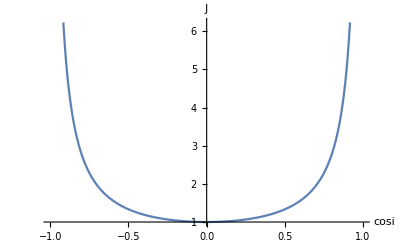

```mathematica
Plot[1/(A^3-A^3 ϵ^2)/.{A->1},{ϵ,-1,1},AxesLabel->{"cosi","J"}]
```

#### Inclination

If we think of planar compact binaries, what’s the Jacobian?

```mathematica
Cosis={A,cosi,θ,ϕ};
AepToCosi={ϵ->(2 cosi)/(1+cosi^2)};
```

```mathematica
Solve[(2 cosi)/(1+cosi^2)==ϵ,cosi]
```

{{cosi→(1-√(1-ϵ^2))/ϵ},{cosi→(1+√(1-ϵ^2))/ϵ}}

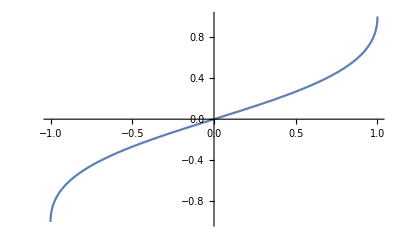

```mathematica
Plot[(1-√(1-ϵ^2))/ϵ,{ϵ,-1,1}]
```

```mathematica
CosiToAep={cosi->(1-√(1-ϵ^2))/ϵ};
```

```mathematica
dCosi=FullSimplify[Det[D[Aeps//.AepToCosi,{Cosis}]],{Element[Aeps,Reals],A>0,-1<=cosi<=1}]
```

-(2 (-1+cosi^2))/((1+cosi^2)^2)

```mathematica
JCosi=Assuming[{A>0,-1<=ϵ<=1, Element[Aeps,Reals]},FullSimplify[Abs[dCosi]//.CosiToAep]]
```

1-ϵ^2+√(1-ϵ^2)

Check the χ parametrization.

```mathematica
CosiToAchi=Join[FullSimplify[CosiToAep//.AepToAchi,{Ahat>0,-Pi/4<=χ<=Pi/4, Element[Aeps,Reals]}],AepToAchi]
```

{cosi→Cot[χ] (1-√(1-Tan[χ]^2)),A→Ahat Cos[χ],ϵ→Tan[χ]}

```mathematica
AchiToCosi=Join[FullSimplify[AchiToAep//.AepToCosi,{A>0,-1<=cosi<=1, Element[Aeps,Reals]}],AchiToAep]
```

{Ahat→A √(1+(4 cosi^2)/((1+cosi^2)^2)),χ→ArcTan[(2 cosi)/(1+cosi^2)],Ahat→A √(1+ϵ^2),χ→ArcTan[ϵ]}

```mathematica
FullSimplify[Cosis//.CosiToAchi,{Ahat>0,-Pi/4<=χ<=Pi/4}]
```

{Ahat Cos[χ],Cot[χ] (1-√(1-Tan[χ]^2)),θ,ϕ}

Doesn’t seem like cos ι has a nice form in terms of χ.

```mathematica
dCosi2=FullSimplify[Det[D[Achis//.AchiToCosi,{Cosis}]],{Element[Aeps,Reals],Ahat>0,-1<=cosi<=1}]
```

-(2 (-1+cosi^2))/((1+cosi^2) √(1+6 cosi^2+cosi^4))

```mathematica
JCosi2=Assuming[{Ahat>0,-Pi/4<=χ<=Pi/4, Element[Aeps,Reals]},FullSimplify[Abs[dCosi2]//.CosiToAchi]]
```

Abs[(-1+Tan[χ]^2+√(1-Tan[χ]^2))/((-1+√(1-Tan[χ]^2)) √(-Csc[χ]^2 (1+2 Cot[χ]^2 (-1+√(1-Tan[χ]^2)))))]

### Coordinate transformation plots

```mathematica
Simplify[ϵ//.AepToAxAy]
```

(√((Acy+Apx)^2+(Acx-Apy)^2)-√((Acy-Apx)^2+(Acx+Apy)^2))/(√((Acy+Apx)^2+(Acx-Apy)^2)+√((Acy-Apx)^2+(Acx+Apy)^2))

```mathematica
Simplify[ϵ//.AepToCphi//.CphiToAphi//.{Ap->1,Ac->1}]
```

(-√(1-Sin[φc-φp])+√(1+Sin[φc-φp]))/(√(1-Sin[φc-φp])+√(1+Sin[φc-φp]))

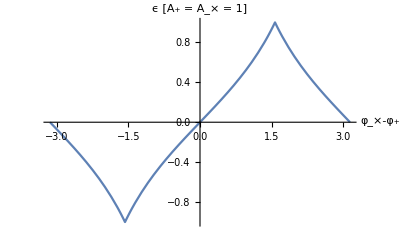

```mathematica
Plot[(-√(1-Sin[φc-φp])+√(1+Sin[φc-φp]))/(√(1-Sin[φc-φp])+√(1+Sin[φc-φp]))/.(φc-φp)->Δφ,{Δφ,-Pi,Pi},AxesLabel->{"φ_×-φ_+","ϵ [A_+ = A_× = 1]"}]
```

```mathematica
Solve[ϵ==-(2 cosi)/(1+cosi^2), cosi]
```

{{cosi→(-1-√(1-ϵ^2))/ϵ},{cosi→(-1+√(1-ϵ^2))/ϵ}}

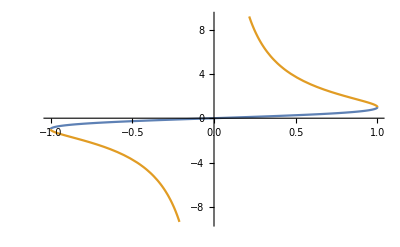

```mathematica
Plot[{(1-√(1-ϵ^2))/ϵ,(1+√(1-ϵ^2))/ϵ},{ϵ,-1,1}]
```

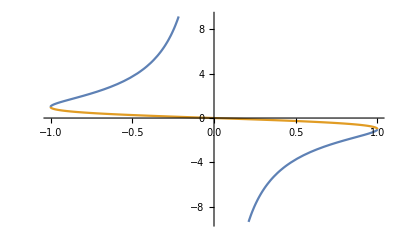

```mathematica
Plot[{(-1-√(1-ϵ^2))/ϵ,(-1+√(1-ϵ^2))/ϵ},{ϵ,-1,1}]
```

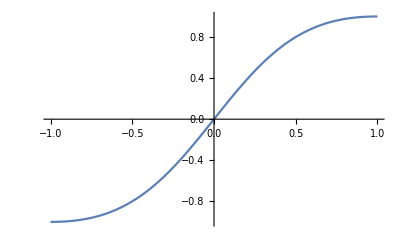

```mathematica
Plot[(2 cosi)/(1+cosi^2),{cosi,-1,1}]
```

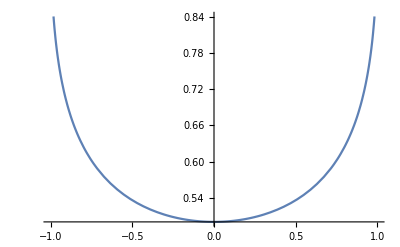

```mathematica
Plot[Abs[(-1+√(1-ϵ^2))/ϵ^2],{ϵ,-1,1}]
```

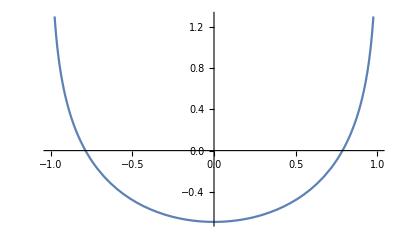

```mathematica
Plot[-2 Log[Abs[ϵ]]+Log[Abs[-1+1/(√(1-ϵ^2))]],{ϵ,-1,1}]
```